## 1. Apperatefunktion

```mathematica
d0={{"λ", "U0", "Umag", "Ugelb", "Um+g"}, {400, 0.184, 0.117, 0.045, 0.041}, {410, 0.246, 0.150, 0.048, 0.042}, {420, 0.326, 0.179, 0.045, 0.041}, {430, 0.418, 0.201, 0.046, 0.042}, {440, 0.547, 0.217, 0.046, 0.042}, {450, 0.698, 0.218, 0.046, 0.041}, {460, 0.906, 0.204, 0.047, 0.041}, {470, 1.117, 0.163, 0.048, 0.042}, {480, 1.326, 0.131, 0.089, 0.046}, {490, 1.546, 0.098, 0.314, 0.051}, {500, 1.883, 0.074, 0.709, 0.053}, {510, 2.310, 0.064, 1.233, 0.053}, {520, 2.709, 0.057, 1.827, 0.052}, {530, 3.084, 0.051, 2.302, 0.048}, {540, 3.438, 0.048, 2.668, 0.047}, {550, 3.784, 0.049, 2.945, 0.047}, {560, 4.12, 0.054, 3.356, 0.051}, {570, 4.47, 0.054, 3.764, 0.052}, {580, 4.80, 0.058, 3.801, 0.054}, {590, 5.13, 0.088, 4.29, 0.077}, {600, 5.45, 0.308, 4.47, 0.237}};
```

## Fehler

```mathematica
dλ=0.2;
dU=0.002;(*VC230*)
```

## 2. Diode offset

```mathematica
off=0.029;
```

## 3. Farbfilter

```mathematica
d1={{"λ", "U1", "U2", "U1+2"}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}, {1, 1, 1, 1}};
```

## 4. Farblösung

```mathematica
d2={{"λ", "U3"}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}, {1, 1}};
```

```mathematica
c=1;dc=0;
```

```mathematica
x=1;dx=0;
```

## Auswertung

```mathematica
Needs["PlotLegends`"]
```

PlotLegend::shdw: Symbol PlotLegend appears in multiple contexts PlotLegends`Global`; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

```mathematica
<<"Labor.m"
```

```mathematica
ad1=Table[Optic`Adsorbance[d0[[x,2]]-off,d0[[x,3]]-off,dU,dU],{x,2,22}];
ad2=Table[Optic`Adsorbance[d0[[x,2]]-off,d0[[x,4]]-off,dU,dU],{x,2,22}];ad12=Table[Optic`Adsorbance[d0[[x,2]]-off,d0[[x,5]]-off,dU,dU],{x,2,22}];
ad1t=Table[Optic`Transmission[d0[[x,2]]-off,d0[[x,3]]-off,dU,dU],{x,2,22}];
ad2t=Table[Optic`Transmission[d0[[x,2]]-off,d0[[x,4]]-off,dU,dU],{x,2,22}];
ad12t=Table[Optic`Transmission[d0[[x,2]]-off,d0[[x,5]]-off,dU,dU],{x,2,22}]
```

{{0.0774194,0.0139022},{0.0599078,0.00976874},{0.040404,0.00700609},{0.033419,0.00531321},{0.0250965,0.0039579},{0.0179372,0.00304316},{0.013683,0.00231171},{0.0119485,0.0018602},{0.0131072,0.00156223},{0.0145023,0.00133751},{0.012945,0.00109271},{0.0105217,0.000886034},{0.00858209,0.000752673},{0.00621931,0.000658736},{0.00528014,0.00058978},{0.00479361,0.000535176},{0.00537766,0.000491507},{0.00517901,0.000452681},{0.00523999,0.000421396},{0.00940992,0.000395769},{0.0383693,0.000383091}}

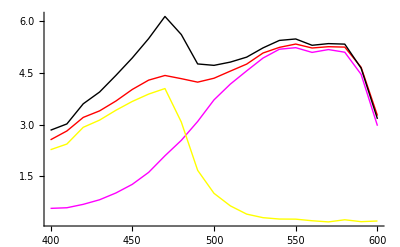

-Graphics-

```mathematica
Show[ListPlot[{Table[{d0[[x+1,1]],ad1[[x,1]]},{x,1,21}],Table[{d0[[x+1,1]],ad2[[x,1]]},{x,1,21}],Table[{d0[[x+1,1]],ad12[[x,1]]},{x,1,21}],Table[{d0[[x+1,1]],ad1[[x,1]]+ad2[[x,1]]},{x,1,21}]},PlotLegend->{"mag","yel","kombi","add"},PlotStyle-> {Magenta,Yellow,Red,Black},Joined->True]]
```

```mathematica
Show[ListPlot[{Table[{d0[[x+1,1]],ad1t[[x,1]]},{x,1,21}],Table[{d0[[x+1,1]],ad2t[[x,1]]},{x,1,21}],Table[{d0[[x+1,1]],ad12t[[x,1]]},{x,1,21}],Table[{d0[[x+1,1]],ad1t[[x,1]]*ad2t[[x,1]]},{x,1,21}]},PlotLegend->{"mag","yel","kombi","add"},PlotStyle-> {Magenta,Yellow,Red,Black},Joined->True]]
```